# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
Get["C:\\Users\\Miguel\\Github\\Entropy\\QMB_offline.wl"];
Needs["MaTeX`"];
```

C:\Users\Miguel\Github\Entropy

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# New functions

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svnt];
svnt[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
```

```mathematica
Clear[svnnot];
svnnot[ini_,L_]:=Module[{rho,λ,purity},
rho=MatrixPartialTrace[Dyad[ini],1,{2^(L/2),2^(L/2)}];
(*purity=Chop[Tr[rho.rho]];*)
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
(*λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}*)
];
```

```mathematica
L=10;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
entropies=ParallelTable[svnnot[i,L],{i,eigenvec},DistributedContexts->Full];
```

```mathematica
data=ParallelTable[{{scaledeigenval[[i]],Chop[entropies][[i]]}},{i,Length[eigenval]}];
(*data2=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,2]]][[i]]}},{i,Length[eigenval]}];*)
```

```mathematica
ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
inirho=Dyad[eigenvec[[10]]];
inirho//Dimensions
```

{1024,1024}

```mathematica
rho=MatrixPartialTrace[inirho,1,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
```

0.735381

```mathematica
rho2=MatrixPartialTrace[inirho,1,{2^(L/2),2^(L/2)}];
```

```mathematica
dA=2^(L/2);
dB=2^(L/2);
```

```mathematica
rhoTensor=ArrayReshape[inirho,{dA,dB,dA,dB}];
rhoReshaped=ArrayReshape[Transpose[rhoTensor,{1,3,2,4}],{dA^2,dB^2}];
{u,s,v}=SingularValueDecomposition[rhoReshaped];
uOps=ArrayReshape[#,{dA,dA}]&/@Transpose[u];
vOps=ArrayReshape[#,{dB,dB}]&/@Transpose[v];
rhoA=Sum[s[[i,i]]*uOps[[i]]*Tr[vOps[[i]]],{i,1,Length[s]}];
```

```mathematica
(*Precompute the scalar coefficients for each term*)
coeffs=Table[s[[i,i]]*Tr[vOps[[i]]],{i,1,Length[s]}];
(*Compute the reduced density matrix by a vectorized sum*)
rhoA=Total[MapThread[#1*#2&,{coeffs,uOps}]];
```

```mathematica
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rhoA]]]]]
```

0.735381

```mathematica
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho2]]]]]
```

0.735381

```mathematica
Clear[svnnotb];
svnnotb[ini_,L_]:=Module[{rho,λ,purity,dA=2^(L/2),dB=2^(L/2),u,s,v,uOps,vOps,rhoA,rhoReshaped,inirho=Dyad[ini]},
rhoReshaped=ArrayReshape[Transpose[ArrayReshape[inirho,{dA,dB,dA,dB}],{1,3,2,4}],{dA^2,dB^2}];
{u,s,v}=SingularValueDecomposition[rhoReshaped];
uOps=ArrayReshape[#,{dA,dA}]&/@Transpose[u];
vOps=ArrayReshape[#,{dB,dB}]&/@Transpose[v];
rhoA=Sum[s[[i,i]]*uOps[[i]]*Tr[vOps[[i]]],{i,Length[s]}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rhoA]]]]]
];
```

```mathematica
svnnotb[eigenvec[[10]],L]
```

0.735381

```mathematica
entropiesb=ParallelTable[svnnotb[i,L],{i,eigenvec}];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.2\WolframKernel" -noicon -noinit -subkernel -wstp,665,15].

KernelObject::rdead: Discarding kernel 1 (Local (14)).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.2\WolframKernel" -noicon -noinit -subkernel -wstp,669,19].

KernelObject::rdead: Discarding kernel 5 (Local (14)).

LaunchKernels::clone: dead kernel 1 (Local (14)) resurrected as kernel 16 (Local (14)).

LaunchKernels::clone: dead kernel 5 (Local (14)) resurrected as kernel 17 (Local (14)).

$Aborted

```mathematica
entropiesb[[1]]
entropiesb[[10]]
```

0.00167675

0.699169

```mathematica
entropies[[1]]
```

0.61708

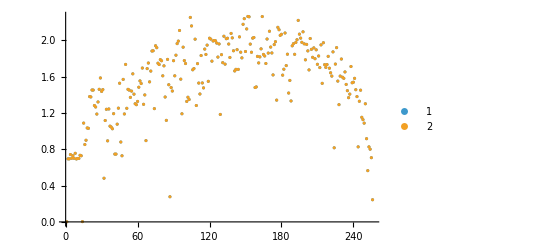

```mathematica
ListPlot[{entropies,entropiesb},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Chop[entropies-entropiesb]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}